# Form Finding with Membrane Equilibrium Analysis (MEA)

## Init (Run First)

### Packages

```mathematica
Needs["NDSolve`FEM`"];
```

### Simboli

```mathematica
Needs["Notation`"];
```

#### Coordinate Cartesiane

```mathematica
Symbolize[z^α];AddInputAlias["za"->z^α];
```

```mathematica
Symbolize[z^i];AddInputAlias["zi"->z^i];
```

```mathematica
Symbolize[z^i_];AddInputAlias["czi"->z^■];
```

```mathematica
Symbolize[Subscript[z, P_]^i_];AddInputAlias["fzi"->z_■^□];
```

```mathematica
z^α/:{z^α}={z^1,z^2};
z^i/:{z^i}=Join[{z^α},{z^3}];
```

```mathematica
Symbolize[(z̃)^α];AddInputAlias["pza"->(z̃)^α];
```

```mathematica
Symbolize[(z̃)^i];AddInputAlias["pzi"->(z̃)^i];
```

#### Base usuale in ℝ^3

```mathematica
Symbolize[Subscript[ê, i_]];AddInputAlias["lei"->ê_■];
```

```mathematica
Symbolize[ê^i_];AddInputAlias["uei"->ê^■];
```

```mathematica
$Assumptions={(Subscript[ê, 1]|Subscript[ê, 2]|Subscript[ê, 3]|ê^1|ê^2|ê^3)∈Vectors[3,Reals]};
```

```mathematica
InfixNotation[·,Dot]
```

```mathematica
(*Subscript[ê, 1]/:0 Subscript[ê, 1]:=UnderBar[0]*)
Subscript[ê, 1]/:Subscript[ê, 1]^2:=1
Subscript[ê, 1]/:Subscript[ê, 1].Subscript[ê, 1]:=1
Subscript[ê, 1]/:Subscript[ê, 1].Subscript[ê, 2]:=0
Subscript[ê, 1]/:Subscript[ê, 1].Subscript[ê, 3]:=0

(*Subscript[ê, 1]/:Subscript[ê, 1]×UnderBar[0]:=UnderBar[0]*)
Subscript[ê, 1]/:Subscript[ê, 1]×Subscript[ê, 2]:=Subscript[ê, 3]
Subscript[ê, 1]/:Subscript[ê, 1]×Subscript[ê, 3]:=-Subscript[ê, 2]
Subscript[ê, 1]/:Subscript[ê, 1]×Subscript[ê, 1]:=0
```

```mathematica
(*Subscript[ê, 2]/:0 Subscript[ê, 2]:=UnderBar[0]*)
Subscript[ê, 2]/:Subscript[ê, 2]^2:=1
Subscript[ê, 2]/:Subscript[ê, 2].Subscript[ê, 1]:=0
Subscript[ê, 2]/:Subscript[ê, 2].Subscript[ê, 2]:=1
Subscript[ê, 2]/:Subscript[ê, 2].Subscript[ê, 3]:=0

(*Subscript[ê, 2]/:Subscript[ê, 2]×UnderBar[0]:=UnderBar[0]*)
Subscript[ê, 2]/:Subscript[ê, 2]×Subscript[ê, 3]:=Subscript[ê, 1]
Subscript[ê, 2]/:Subscript[ê, 2]×Subscript[ê, 1]:=-Subscript[ê, 3]
Subscript[ê, 2]/:Subscript[ê, 2]×Subscript[ê, 2]:=0
```

```mathematica
(*Subscript[ê, 3]/:0 Subscript[ê, 3]:=UnderBar[0]*)
Subscript[ê, 3]/:Subscript[ê, 3]^2:=1
Subscript[ê, 3]/:Subscript[ê, 3].Subscript[ê, 1]:=0
Subscript[ê, 3]/:Subscript[ê, 3].Subscript[ê, 2]:=0
Subscript[ê, 3]/:Subscript[ê, 3].Subscript[ê, 3]:=1

(*Subscript[ê, 3]/:Subscript[ê, 3]×UnderBar[0]:=UnderBar[0]*)
Subscript[ê, 3]/:Subscript[ê, 3]×Subscript[ê, 1]:=Subscript[ê, 2]
Subscript[ê, 3]/:Subscript[ê, 3]×Subscript[ê, 2]:=-Subscript[ê, 1]
Subscript[ê, 3]/:Subscript[ê, 3]×Subscript[ê, 3]:=0
```

```mathematica
Notation[Subscript[ℬ, n_] ⟺ Base[n_]]
```

```mathematica
Base[n_]:=Apply[TensorProduct,(Array[List@@{##}&, Table[3,n]]/.{1->Subscript[ê, 1],2->Subscript[ê, 2],3->Subscript[ê, 3]}),{-2}];
```

```mathematica
InfixNotation[⊗,TensorProduct]
```

#### Coordinate Curvilinee

```mathematica
Symbolize[ϑ^i_];AddInputAlias["ti"->ϑ^■];
```

```mathematica
Symbolize[Subscript[ϑ, P_]^i_];AddInputAlias["fti"->ϑ_■^□];
```

```mathematica
χ={ϑ^1,ϑ^2};
```

#### Parametrizzazione

```mathematica
Symbolize[𝓏̃]; AddInputAlias["pz"->𝓏̃];
```

```mathematica
Symbolize[𝕫̃]; AddInputAlias["z3"->𝕫̃];
```

```mathematica
Symbolize[(z̃)^i_];AddInputAlias["pzi"->(z̃)^□];
```

```mathematica
𝓏̃={(z̃)^1,(z̃)^2};
𝕫̃=Join[𝓏̃,{(z̃)^3}];
```

#### Superfici, Contorni, Regioni ed Intervalli

```mathematica
Symbolize[𝒮^i_];AddInputAlias["Si"->𝒮^□];
```

```mathematica
Symbolize[Subscript[𝒞, 𝒮^i_]];AddInputAlias["CSi"->𝒞_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[ℛ, 𝒮^i_]];AddInputAlias["RSi"->ℛ_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[ℐ, 𝒮^i_]];AddInputAlias["ISi"->ℐ_(𝒮^□)];
```

#### Domini

```mathematica
Symbolize[Subscript[Ω, 𝒮^i_]];AddInputAlias["WSi"->Ω_(𝒮^□)];
```

#### Frontiere

```mathematica
Symbolize[Subscript[Γ, 𝒮^i_]];AddInputAlias["GSi"->Γ_(𝒮^□)];
```

... Dirichelet

```mathematica
Symbolize[Subscript[Γ, 𝒮^i_]^D];AddInputAlias["GDSi"->Γ_(𝒮^□)^D];
```

```mathematica
Symbolize[Subscript[εΓ, 𝒮^i_]^D];AddInputAlias["eGDSi"->εΓ_(𝒮^□)^D];(* traccia *)
```

... Neumann

```mathematica
Symbolize[Subscript[Γ, 𝒮^i_]^N];AddInputAlias["GNSi"->Γ_(𝒮^□)^N];
```

```mathematica
Symbolize[Subscript[εΓ, 𝒮^i_]^N];AddInputAlias["eGNSi"->εΓ_(𝒮^□)^N];(* traccia *)
```

#### f

(descrizione alla Monge (z^1, z^2, f_(𝒮^i)))

```mathematica
Symbolize[Subscript[f, 𝒮^i_]];AddInputAlias["fSi"->f_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[f, 𝒮^i_]^D];AddInputAlias["fDSi"->f_(𝒮^□)^D];
```

```mathematica
Symbolize[Subscript[f, 𝒮^i_]^N];AddInputAlias["fNSi"->f_(𝒮^□)^N];
```

```mathematica
Symbolize[Subscript[f, 𝒮^i_]];AddInputAlias["$fSi"->f_(𝒮^□)];
```

base naturale e base duale

```mathematica
Symbolize[Subscript[a, i_]];AddInputAlias["lai"->a_■]
```

```mathematica
Symbolize[Subscript[a, i]];AddInputAlias["la"->Subscript[a, i]]
```

```mathematica
Symbolize[Subscript[a, ij]];AddInputAlias["laM"->Subscript[a, ij]]
```

```mathematica
Symbolize[a^i_];AddInputAlias["uai"->a^■]
```

```mathematica
Symbolize[a^i];AddInputAlias["ua"->a^i]
```

```mathematica
Symbolize[a^ij];AddInputAlias["uaM"->a^ij]
```

#### F

```mathematica
Symbolize[Subscript[F, 𝒮^i_]];AddInputAlias["FSi"->F_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[F, 𝒮^i_]^D];AddInputAlias["FDSi"->F_(𝒮^□)^D];
```

```mathematica
Symbolize[Subscript[F, 𝒮^i_]^N];AddInputAlias["FNSi"->F_(𝒮^□)^N];
```

```mathematica
Symbolize[Subscript[F, 𝒮^i_]];AddInputAlias["$FSi"->F_(𝒮^□)];
```

base naturale e base duale

```mathematica
Symbolize[Subscript[A, i_]];AddInputAlias["lAi"->A_■]
```

```mathematica
Symbolize[Subscript[A, i]];AddInputAlias["lA"->Subscript[A, i]]
```

```mathematica
Symbolize[A^i_];AddInputAlias["uAi"->A^■]
```

```mathematica
Symbolize[A^i];AddInputAlias["uA"->A^i]
```

#### Mesh

```mathematica
Symbolize[Subscript[𝒯, 𝒮^i_]];AddInputAlias["TSi"->𝒯_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[𝒯, 𝒮^i_]^D];AddInputAlias["TDSi"->𝒯_(𝒮^□)^D];
```

```mathematica
Symbolize[Subscript[𝒯, 𝒮^i_]^N];AddInputAlias["TNSi"->𝒯_(𝒮^□)^N];
```

#### Tensione

```mathematica
Symbolize[S^{i_,j_}];AddInputAlias["SPu"->S^{■,□}]
```

```mathematica
Symbolize[S̃];AddInputAlias["pS"->S̃]
```

```mathematica
Symbolize[(S̃)^{i_,j_}];AddInputAlias["pSPu"->(S̃)^{■,□}]
```

```mathematica
Symbolize[Subscript[î, a_]];AddInputAlias["lia"->î_■]
Symbolize[î^a_];AddInputAlias["uia"->î^■]
```

### Tools

```mathematica
ArcDivide[{z1func_, z2func_ }, {par_, a_,b_}, n_]:=Module[
{Δs, len, arc,step, du,sol},
len=ArcLength[{z1func, z2func }, {par, a,b}, Method->"NIntegrate"];
Δs[start_?NumberQ,end_?NumberQ]:=ArcLength[{z1func,z2func}, {par,start,end}, Method->"NIntegrate"];
arc=len/(n-1);
sol=Join[{a},Table[du/.First[FindRoot[Δs[a,du]==i arc, {du,a,b}]],{i,1,n-2}],{b}];
Transpose[{z1func,z2func}/.par->sol]
]
```

```mathematica
ArcDivide[{z1func_, z2func_ }, par_∈Interval[{ a_,b_}], n_]:=ArcDivide[{z1func, z2func}, {par, a,b}, n]
```

### Mod

```mathematica
mod[u_]:=Sqrt[u.u]
```

### PBezier

```mathematica
AddInputAlias["ff"->OverTilde[□]]
```

```mathematica
PBezier[t_,n_,γ_, v_:Automatic]:=Module[
{b,vtmp,rtmp,r,f,m,i,j},
For[i=0,i≤n,i++,
b[i]=Factorial[n]/(Factorial[i]Factorial[n-i])(1-t)^(n-i) t^i (*BernsteinBasis[n,i,t]*)
];
vtmp=Table[0,{i,1,n+1}];
If[v≠Automatic,
vtmp=Rescale[v],
For[i=0,i≤n,i++,vtmp[[i+1]]=i/n]
];
For[i=0,i≤n,i++,
rtmp=t-vtmp[[i+1]];
For[j=0,j≤i-1,j++, 
rtmp=rtmp+2 b[j](i-j)/n];
f[i]=rtmp^2-(t-i/n)^2;
r[i]=Sqrt[(t-i/n)^2+γ f[i]]
];
m[0]=1/2+n(r[1]-r[0])/2;
For[i=1,i≤n-1,i++,
m[i]=n (r[i-1]-2 r[i]+r[i+1])/2];
m[n]=1/2-n(r[n]-r[n-1])/2;
Table[m[i],{i,0,n}]
]
ProxBezier=(PBezier[λ,2,γ])//Simplify; (* prevedere il caso semplice: lineare tra {ϑ̲, g̲} e {ϑ̄, ḡ}*)
(*p[λ_,γ_]=Sum[ProxBezier[[i]]V[i-1],{i,1,3}]//Chop;*)
```

### Symbols

```mathematica
<<Notation`
```

#### Cartesian Coordinates and Basis Vectors

covariante ≡ controvariante

```mathematica
Symbolize[Subscript[z, _]];AddInputAlias["z_"->z_□];
OverTilde[z][i_?IntegerQ]:=ToExpression[SubscriptBox["z",ToString[Abs[i]]]]
```

```mathematica
Symbolize[(e⃗)__];AddInputAlias["e_"->(e⃗)_□];
OverTilde[e][i_?IntegerQ]:=ToExpression[SubscriptBox[OverscriptBox["e","⇀"],ToString[Abs[i]]]]
```

```mathematica
{Subscript[e⃗, 1]}^=UnitVector[3,1];
{Subscript[e⃗, 2]}^=UnitVector[3,2];
{Subscript[e⃗, 3]}^=UnitVector[3,3];
```

#### Skew Coordinates and Basis Vectors

```mathematica
Symbolize[x^_];AddInputAlias["x^"->x^□];
Symbolize[Subscript[x, _]];AddInputAlias["x_"->x_□];
OverTilde[x][i_/;i>0&&IntegerQ[i]]:=ToExpression[SuperscriptBox["x",ToString[i]]]
OverTilde[x][i_/;i<0&&IntegerQ[i]]:=ToExpression[SubscriptBox["x",ToString[Abs[i]]]]
```

```mathematica
Symbolize[(a⃗)__];AddInputAlias["a_"->(a⃗)_□];
OverTilde[a][i_/;i<0&&IntegerQ[i]]:=ToExpression[SubscriptBox[OverscriptBox["a","⇀"],ToString[Abs[i]]]]
Symbolize[(a⃗)^_];AddInputAlias["a^"->(a⃗)^□];
OverTilde[a][i_/;i>0&&IntegerQ[i]]:=ToExpression[SuperscriptBox[OverscriptBox["a","⇀"],ToString[Abs[i]]]]
```

```mathematica
Symbolize[a_(..)];Symbolize[a^(..)];
```

#### Curvilinear Coordinates (vault) and Basis Vectors

```mathematica
Symbolize[ϑ^_];AddInputAlias["q^"->ϑ^□];
Symbolize[Subscript[ϑ, _]];AddInputAlias["q_"->ϑ_□];
OverTilde[ϑ][i_/;i>0&&IntegerQ[i]]:=ToExpression[SuperscriptBox["ϑ",ToString[i]]]
OverTilde[ϑ][i_/;i<0&&IntegerQ[i]]:=ToExpression[SubscriptBox["ϑ",ToString[Abs[i]]]]
```

```mathematica
Symbolize[(g⃗)__];AddInputAlias["g_"->(g⃗)_□];
OverTilde[g][i_/;i<0&&IntegerQ[i]]:=ToExpression[SubscriptBox[OverscriptBox["g","⇀"],ToString[Abs[i]]]]
Symbolize[(g⃗)^_];AddInputAlias["g^"->(a⃗)^□];
OverTilde[g][i_/;i>0&&IntegerQ[i]]:=ToExpression[SuperscriptBox[OverscriptBox["g","⇀"],ToString[Abs[i]]]]
Symbolize[g_(..)];Symbolize[g^(..)];
```

#### Unit Vectors

```mathematica
Symbolize[(h⃗)__];AddInputAlias["h_"->(h⃗)_□];
```

```mathematica
OverTilde[h][i_/;i>0&&IntegerQ[i]]:=ToExpression[SubscriptBox[OverscriptBox["h","⇀"],ToString[Abs[i]]]]
```

```mathematica
Symbolize[(k⃗)__];AddInputAlias["k_"->(k⃗)_□];
OverTilde[k][i_/;i>0&&IntegerQ[i]]:=ToExpression[SubscriptBox[OverscriptBox["k","⇀"],ToString[Abs[i]]]]
```

#### Boundary

```mathematica
Symbolize[(∂γ)__];AddInputAlias["bdi"->(∂γ)__]
OverTilde[γ][i_/;i>0&&IntegerQ[i]]:=ToExpression[SubscriptBox[OverscriptBox[RowBox[{"∂","γ"}],"⏜"],ToString[i]]]
```

```mathematica
Symbolize[∂Ω];AddInputAlias["bd"->∂Ω]
```

#### Splines

```mathematica
Symbolize[Subscript[α, _]];AddInputAlias["a_"->α_□];
OverTilde[α][i_/;i>0&&IntegerQ[i]]:=ToExpression[SubscriptBox["α",ToString[i]]]
```

### Cartesian unit base vectors

```mathematica
Subscript[e, 1]={1,0,0};
Subscript[e, 2]={0,1,0};
Subscript[e, 3]={0,0,1};
```

### 3D Rotation Matrix

```mathematica
Rx[ϕ_]:={{1,0,0},{0,Cos[ϕ],-Sin[ϕ]},{0,Sin[ϕ],Cos[ϕ]}};
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0},{-Sin[ϕ],0,Cos[ϕ]}};
Rz[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}};
```

## Solution (parametric_vertical loads)

## DATA

#### Geometrical data [m]

```mathematica
b=4.;
l=6.5;
Subscript[h, i]=.8;
Subscript[s, a]=.1;
Subscript[h, e]=Subscript[h, i]+Subscript[s, a];
γ=0;
Subscript[h, s]=0.0;
𝓉=.12;
ℓ=l+𝓉;
𝒷=b+𝓉;
```

#### Assigned Variables

```mathematica
t1=20.;
t2=20.;
t3=15.;
```

#### Materials [kN/m^3]

```mathematica
Subscript[ρ, a]=18.0; 
g=9.81;
𝓌=Subscript[ρ, a] 𝓉;
```

#### FEM Mesh Size

```mathematica
size=0.5;
```

Program

## GEOMETRY

### Arch

```mathematica
EqCircle[x1_,x3_]=(x1-x10)^2+(x3-x30)^2==r^2;
```

```mathematica
MyCircle[pt1_,pt2_,pt3_]:=EqCircle[x1,x3]/.First[Solve[{EqCircle@@pt1,EqCircle@@pt2,EqCircle@@pt3,r>0},{x10,x30,r}]//Quiet]
```

#### Intrados surface

```mathematica
Intradox=MyCircle[{-l/2,0},{0,Subscript[h, i]},{l/2,0}];
```

```mathematica
SolCircleIntradox=First[Solve[{EqCircle@@{-l/2,0},EqCircle@@{0,Subscript[h, i]},EqCircle@@{l/2,0},r>0},{x10,x30,r}]]//Quiet;
```

```mathematica
solI=Solve[Intradox,x3]//Quiet;
```

```mathematica
gI=x3/.solI[[2]];
```

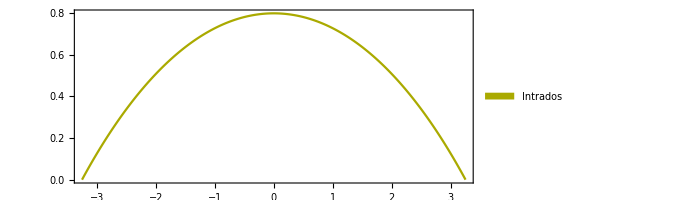

```mathematica
Subscript[𝒮, i]=RegionPlot[ImplicitRegion[Intradox,{{x1,-l/2,l/2},{x3,0,Subscript[h, i]}}],AspectRatio->Automatic,PlotLegends->{"Intrados"}, PlotStyle->Darker[Yellow],BoundaryStyle->Darker[Yellow]]
```

#### Estradox surface

```mathematica
Extradox=((x1-x10)^2+(x3-x30)^2==(r+Subscript[s, a])^2)/.SolCircleIntradox;
```

```mathematica
solE=Solve[Extradox,x3]//Quiet;
```

```mathematica
gE=x3/.solE[[2]];
```

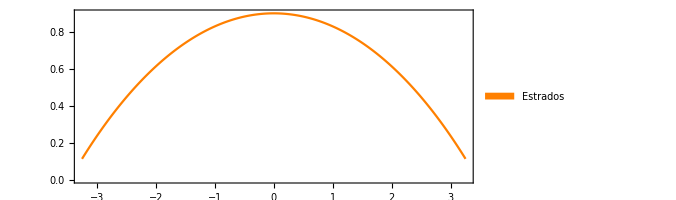

```mathematica
Subscript[𝒮, e]=RegionPlot[ImplicitRegion[Extradox,{{x1,-l/2,l/2},{x3,0,Subscript[h, e]}}],AspectRatio->Automatic,PlotLegends->{"Estrados"},PlotStyle->Orange,BoundaryStyle->Orange]
```

#### Reference surface

```mathematica
MMedium=((x1-x10)^2+(x3-x30)^2==(r+Subscript[s, a]/2)^2)/.SolCircleIntradox;
```

```mathematica
solM=Solve[MMedium,x3]//Quiet;
```

```mathematica
gM=x3/.solM[[2]];
```

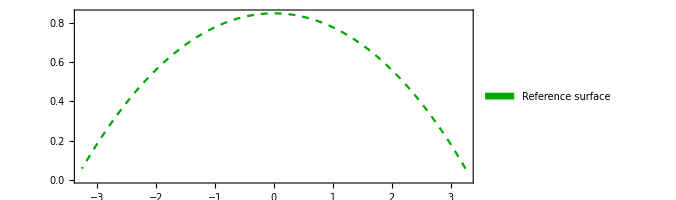

```mathematica
Subscript[𝒮, m]=RegionPlot[ImplicitRegion[MMedium,{{x1,-l/2,l/2},{x3,0,(Subscript[h, i]+Subscript[s, a]/2)}}],AspectRatio->Automatic,PlotLegends->{"Reference surface"},PlotStyle->Darker[Green],BoundaryStyle->Directive[Dashed,Darker[Green]]]
```

### Total Surface

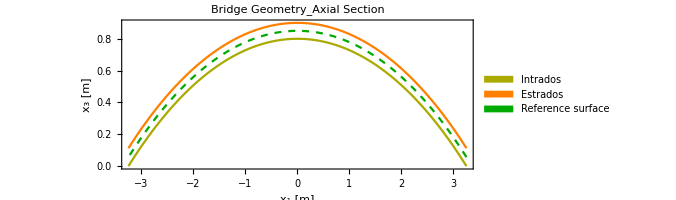

```mathematica
BridgeGeometry=Show[{Subscript[𝒮, i],Subscript[𝒮, e],Subscript[𝒮, m]},FrameLabel->{"x_1 [m]","x_3 [m]"},PlotLabel->Style["Bridge Geometry_Axial Section",Plain,Bold,FontSize->14],LabelStyle->Directive[Black,Bold],PlotRange->All]
```

## PARABOLOID (𝒮 )

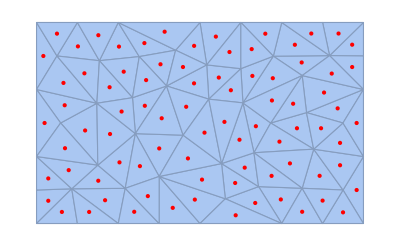

```mathematica
ℛ=ImplicitRegion[-l/2≤ x1≤ l/2&&-b/2≤ x2≤ b/2, {{x1,-l/2,l/2},{x2,-b/2,b/2}}];
Ω=DiscretizeRegion[ℛ,"MeshOrder"->2,MaxCellMeasure->size];
CentroidMeshPoints=AnnotationValue[{Ω,2},MeshCellCentroid];
Show[Ω,Graphics[{Red,Point[%]}]]
```

#### Airy Stress Function

```mathematica
𝒮[σ_,α_]:={{x1,x2,σ(1/8(1(b^2-4x2^2)+α(l^2-4x1^2)))},{x1,x2}∈Ω}
𝓈[σ_,α_]:=𝒮[σ,α][[1]]
```

## TRANSVERSAL EQUILIBRIUM

#### Second derivate of F

```mathematica
Subscript[F, 𝒮22]=D[𝒮[σ,α][[1,3]], {x2,2}];
Subscript[F, 𝒮11]=D[𝒮[σ,α][[1,3]], {x1,2}];
Subscript[F, 𝒮12]=D[𝒮[σ,α][[1,3]], x1,x2];
```

#### Differential equation (𝒻 unknown)

```mathematica
EqDiff[σ_,α_]=((D[Subscript[f, 𝒮^1][x1,x2],{x2,2}] Subscript[F, 𝒮11]+
D[Subscript[f, 𝒮^1][x1,x2],{x1,2}] Subscript[F, 𝒮22]-
2 D[Subscript[f, 𝒮^1][x1,x2],x1,x2] Subscript[F, 𝒮12])-𝓌);
```

#### Boundary conditions

```mathematica
bcs=DirichletCondition[Subscript[f, 𝒮^1][x1,x2]==gI,True];
```

#### Equilibrium solution

```mathematica
Subscript[h, 𝒮^1]=Subscript[f, 𝒮^1]/.ParametricNDSolve[
{EqDiff[σ,α]==0,bcs},Subscript[f, 𝒮^1],{x1,x2}∈Ω,{σ,α},
Method->{"FiniteElement",
"MeshOptions"->{"MeshOrder"->2,MaxCellMeasure->size},
"IntegrationOrder"->4,
"InterpolationOrder"->{Subscript[f, 𝒮^1]->2}}];
```

```mathematica
𝒻[σ_,α_]=(Subscript[h, 𝒮^1][σ,α])[x1,x2];
```

```mathematica
Manipulate[Plot3D[{1.6,
Evaluate[𝒻[σ,α]]},{x1,x2}∈Ω, AxesStyle->Directive[Black, 14],PlotPoints->Automatic,PlotStyle->{Directive[Red,Opacity[0.3]],Directive[Gray,Opacity[0.3]]},Mesh->True,BoundaryStyle->Thickness[0.005],AxesLabel->{"x_1[m]","x_2[m]","x_3[m]"},BoxRatios->Automatic,Boxed->True],{{σ,6.1},.01,10.},
{{α,.8},0.1,1.8}]
```

## 1^st Set of Parameters

## Rule

```mathematica
RuleSol = {σ→3.9,α→0.8};
```

```mathematica
Shell1=𝒻[σ,α]/.RuleSol;
RefShell=Plot3D[Shell1,{x1,x2}∈Ω,LabelStyle->Directive[FontFamily->"Times"],PlotPoints->100,PlotStyle->Directive[Gray,Opacity[0.5]],Mesh->True,BoundaryStyle->Thickness[0.004],AxesLabel->{"x_1[m]","x_2[m]","x_3[m]"},BoxRatios->Automatic,Boxed->False, AxesStyle->Directive[Black, 16],AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]
```

-Graphics3D-

## 2^nd Solution (load assigned on the membrane shape)

## Exact Load Definition

#### Shell and its derivative

```mathematica
𝒻1=D[Shell1, x1];
𝒻2=D[Shell1, x2];
```

#### Shell Basis and Jacobian

```mathematica
Subscript[a, 1]=Subscript[e, 1]+𝒻1 Subscript[e, 3];
Subscript[a, 2]=Subscript[e, 2]+𝒻2 Subscript[e, 3];
𝒥=mod[Subscript[a, 1]×Subscript[a, 2]]//Simplify;
Subscript[a, 3]=(Subscript[a, 1]×Subscript[a, 2])/𝒥//Simplify;
J=√(1+(𝒻11)^2+(𝒻22)^2);
```

#### Exact Shell Load

```mathematica
p=𝓌 𝒥;
```

```mathematica
LoadProfile1=Plot3D[p,{x1,x2}∈Ω,LabelStyle->Directive[16,Black,FontFamily->"Times"],PlotRange->{0,3.0},BoundaryStyle->Directive[Darker[Green],Thickness[0.003]],PlotStyle->Directive[Lighter[Green],Opacity[0.8]],AxesLabel->{"x_1 [m]","x_2 [m]","p [kN/m]"},LabelStyle->Directive[Black, 16],PlotPoints->100,AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]//Quiet
```

-Graphics3D-

#### Differential equation (𝒻 unknown)

```mathematica
EqDiff2[σ_,α_]=((D[Subscript[f, 𝒮^2][x1,x2],{x2,2}] Subscript[F, 𝒮11]+
D[Subscript[f, 𝒮^2][x1,x2],{x1,2}] Subscript[F, 𝒮22]-
2 D[Subscript[f, 𝒮^2][x1,x2],x1,x2] Subscript[F, 𝒮12])-p)//Simplify//Chop//N;
```

#### Boundary conditions

```mathematica
bcs2=DirichletCondition[Subscript[f, 𝒮^2][x1,x2]==gI,True];
```

#### Equilibrium solution

```mathematica
Subscript[h, 𝒮^2]=Subscript[f, 𝒮^2]/.ParametricNDSolve[
{EqDiff2[σ,α]==0,bcs2},Subscript[f, 𝒮^2],{x1,x2}∈Ω,{σ,α},
Method->{"FiniteElement",
"MeshOptions"->{"MeshOrder"->2,MaxCellMeasure->size},
"IntegrationOrder"->4,
"InterpolationOrder"->{Subscript[f, 𝒮^2]->2}}];
```

### THRUST SURFACE 𝒻𝓉 (Optimization of σ, α)

```mathematica
pippo[σ_?NumericQ,α_?NumericQ]:=Module[{h,ω},
h=Subscript[h, 𝒮^2][σ,α][x1,x2];
ω=Ω;
NIntegrate[((h/Shell1)-1)^2,{x1,x2}∈ω]
]//Simplify//Chop//N
```

```mathematica
sol=Assuming[α>0,NMinimize[
pippo[σ,α],
{{σ,5.2,5.3},{α,0.5,0.6}},WorkingPrecision->2]]//Quiet
```

{0.0017,{σ→5.26581,α→0.515855}}

```mathematica
𝒻𝓉[σ_,α_]=(Subscript[h, 𝒮^2][σ,α])[x1,x2];
𝒻𝓉=𝒻𝓉[σ,α]/.sol[[2]];
```

```mathematica
VerticalShell=Plot3D[𝒻𝓉,{x1,x2}∈Ω,LabelStyle->Directive[FontFamily->"Times"],PlotPoints->100,PlotStyle->Directive[Red,Opacity[0.3]],Mesh->True,BoundaryStyle->Thickness[0.004],AxesLabel->{"x_1[m]","x_2[m]","x_3[m]"},BoxRatios->Automatic,Boxed->False, AxesStyle->Directive[Black, 16],AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic];
```

```mathematica
Show[VerticalShell,RefShell]
```

-Graphics3D-